# Laboratory 1 Using of Mathematica Platform – the revision task

1. Select randomly the integer number from interval [0, 20] and check if the selected
number is the prime number. Select randomly the real number from interval
[−100, 100] and check if the selected number is positive.

```mathematica
randint=RandomInteger[{0,20}]
If[PrimeQ[randint],StringForm["Number `` is a prime number.", randint],StringForm["Number `` isn't a prime number.", randint]]
randreal=RandomReal[{-100,100}]
If[randreal>0,StringForm["Number `` is positive.", randreal],StringForm["Number `` isn't positive.", randreal]]
```

11

Number 11 is a prime number.

-53.3475

Number -53.3475 isn't positive.

2. Determine the difference in applying the single, double and triple equality sign ("="
    - assignment, "==" - equality, "===" - identity).

```mathematica
(*'=' is used to assign value or expresion*)
x=5
y=2x+2
```

5

12

```mathematica
(*'==' is checking equality of a number *)
x==6
x==5.0
```

False

True

```mathematica
(* '===' is also checking equality but syntactic one - it checks if expresions are the same*)
x===5
x===5.0
```

True

False

3. By using the definition given below create the list containing 10 first elements of
the Fibonacci sequence.
Create a new 5-element list so that each successive element is the square power of
the previous element. The first element of this list is equal to 3.

```mathematica
a1=1
a2=1
fiboanciList ={a1,a2}
Do[an=a1+a2;a1=a2;a2=an;AppendTo[fiboanciList,an];,{i,3,10}]
Print[fiboanciList]
```

1

1

{1,1}

{1,1,2,3,5,8,13,21,34,55}

```mathematica
myList =Table[3^(2^n),{n,0,4}]
```

{3,9,81,6561,43046721}

4. Determine the difference in applying sign" =" and signs" :=" while defining the
function (in the first case the value of function is calculated when the function is defined, in the second case - the value of function is calculated when the function is executed for the specific argument).

```mathematica
ClearAll[x,y]
x=5
y[x_]:= 2+x
?y
y[x_]=2+x
?y
```

5

7

5. By using instruction ListPlot plot, in the system of coordinates, the elements from the list created in Task 3 and contained the elements of Fibonacci sequence (equalize the units in the axes, label the OX axis as" n" and OY axis as" a[n]", color   the background with lightblue color, mark the points representing the elements of  the sequence with red color and with some sign selected from the palette Special Characters, connect the points with lines).

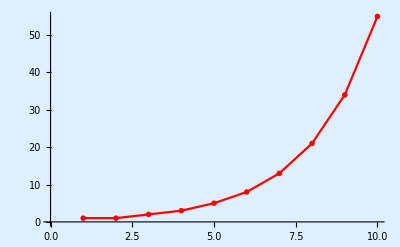

```mathematica
ListPlot[{fiboanciList},Background->LightBlue,PlotMarkers->"OpenMarkers",PlotStyle->Red,Joined->True]
```

7. Draw the graph of function f (x) = sin x for x ∈ [−π, 2π] (color the line of graph 

with green color and mark it with thick and dashed line, color the background with

pink color). Repeat the figure but, instead of full background, fill with pink color the

spaces between the line of graph and OX axis (instructions Filling and FillingStyle).

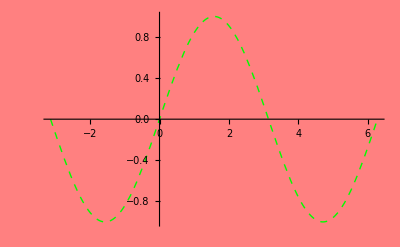

```mathematica
Plot[Sin[x],{x,-Pi,2*Pi},PlotStyle->{Dashed,Thick,Green},Background->Pink]
```

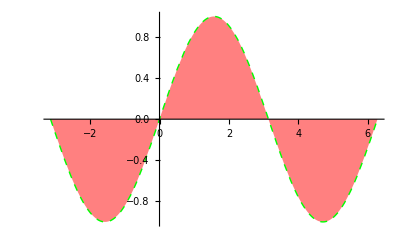

```mathematica
Plot[Sin[x],{x,-Pi,2*Pi},PlotStyle->{Dashed,Thick,Green},Filling->Axis,FillingStyle->Pink]
```

8. Draw the graph of function f (x, y) = sin(x2 + y 2 ) for x, y ∈ [−π, π] (mark the drawn

surface with green color and remove from the figure the mesh and the axes).

```mathematica
Plot3D[Sin[x^2+y^2],{x,-Pi,Pi},{y,-Pi,Pi},PlotStyle->Green,Mesh->None,Axes->False]
```

-Graphics3D-

9.Draw the graph of function given with the aid of parametric equations, in color

selected by you, for t, u ∈ [0, 2π]:


 x = cos t · (3 + cos u),

y = sin t · (3 + cos u), 

z = sin u.

```mathematica
ParametricPlot3D[{Cos[t]*(3+Cos[u]),Sin[t]*(3+Cos[u]),Sin[u]},{u,0,2*Pi},{t,0,2*Pi},PlotStyle->Gray]
```

-Graphics3D-

10. By using instruction Animate animate the graph of function f (x) = esin(tx) in domain

x ∈ [−π, π], in range [0, 3]:



for parameter t changing continuously from 0 to 4;

```mathematica
Animate[Plot[E*Sin[t*x],{x,0,3}],{t,0,4}]
```

for parameter changing from 0 to 8 with step 2;

```mathematica
Animate[Plot[E*Sin[t*x],{x,0,3}],{t,0,8,2}]
```

for parameter t taking the values 0,4,7,8.

```mathematica
Animate[Plot[E*Sin[t*x],{x,0,3}],{t,{0,4,7,8}}]
```

11.  By  using  instruction  Animate  animate  the  graph  of  function  f  (x) = ea  sin (x + y) + b  cos (x − y)
in  domain  x, y ∈ [0, 2 π], in  range [0, 9], for  parameter  a  changing  continuously  from
0  to  1  and  for  parameter  b  changing  from  0  to  9  with  step  2.

```mathematica
Animate[Plot3D[Exp[a*Sin[x+y]+b*Cos[x-y]],{x,0,2*Pi},{y,0,2*Pi},PlotRange->{0,9}]
,{a,0,1},{b,0,9,2}]
```

12.  By  using  instruction  Animate  animate  the  list  containing  the  factorials  of  successive
natural  numbers - number  of  elements  in  the  list  is  the  parameter  changing  from  1
to  10.

```mathematica
Animate[Table[Factorial[n],{n,1,num}],{num,1,10,1}]
```

13.  Repeat  Tasks  10 - 12  by  using  instruction  Manipulate .

```mathematica
Manipulate[Plot[E*Sin[t*x],{x,0,3}],{t,0,4}]
Manipulate[Plot[E*Sin[t*x],{x,0,3}],{t,0,8,2}]
Manipulate[Plot[E*Sin[t*x],{x,0,3}],{t,{0,4,7,8}}]
Manipulate[Plot3D[Exp[a*Sin[x+y]+b*Cos[x-y]],{x,0,2*Pi},{y,0,2*Pi},PlotRange->{0,9}]
,{a,0,1},{b,0,9,2}]
Manipulate[Table[Factorial[n],{n,1,num}],{num,1,10,1}]
```

14.  Create  the  11 - element  list  containing  the  graphs  of  function  f  (x) = sin (tx)  in  domain
x ∈ [−2 π, 2 π], for  parameter  t  taking  the  values 0,1,2,...,10. Animate the elements

of the list by using instruction ListAnimate.

```mathematica
ListAnimate[Table[Plot[Sin[t x],{x,-2 Pi,2 Pi},PlotRange->{-1,1} ],{t,0,10,1}],15,AnimationDirection->ForwardBackward]
```